# HW 3 - Astrophysical Dynamics

FFT Poisson Solver

## Defining constants

```mathematica
nz=32(*Number of zones = nz^3*);
L=4(*Length of the box*);
G=1.0; M=1.0;R=1.0;
```

## Calculations

### Green’s function:

```mathematica
fG=If[(#1==#2==#3==1),0,- G L^2/(1.0 nz^2 (Total[Min[#-1,2nz+1-#]^2&/@{#1,#2,#3}])^.5)]&;
mG=Array[fG,{2nz,2nz,2nz}];(*Values of the Green's function in real space*)
```

```mathematica
FmG=Fourier[mG]; (*Values of the Green's function in fourier space*)
```

### Density function for homogenous sphere:

```mathematica
fP=If[Total[(L/2+(0.5 L)/nz-(# L)/nz)^2&/@{#1,#2,#3}]≤R^2,M/(4.0/3 Pi R^3),0]&;
mn=Array[fP,{2nz,2nz,2nz}];(*Values of the density in real space.*)
```

```mathematica
Fmn=Fourier[mn]; (*Values of the density in fourier space*)
```

### Compiled parallelized code to calculate the density values:

```mathematica
fPc=Compile[{{x, _Integer},{y, _Integer},{z, _Integer},{n,_Integer},{r,_Real},{m,_Real},{l,_Real}},If[(l/2+l/(2n)-(l*x)/n)^2+(l/2+l/(2n)-(l*y)/n)^2+(l/2+l/(2n)-(l*z)/n)^2≤r^2,(0.23873241463784303*m)/r^3,0]]; 

mV=ParallelArray[fPc[#1,#2,#3,nz,R,M,L]&,{2nz,2nz,2nz}];
(*This is the potential in real space*)
```

### Inverse fourier transform of the product

```mathematica
mSol=(2nz)^1.5 Re[InverseFourier[Fmn *FmG]][[1;;nz,1;;nz,1;;nz]];
```

## Plots of analytic vs numerical solution along x-axis

### Numerical solution

```mathematica
A=mSol[[1;;nz,Floor[nz/2],Floor[nz/2]]];X=(Range[nz]-.5)L/nz;
```

### Analytical solution

```mathematica
V[r_]:=If[Abs[r]<R,-G M (3 R^2 - r^2)/(2 R^3),-G M/Abs[r]]
```

### Potential along the x-axis passing through the center of the sphere:

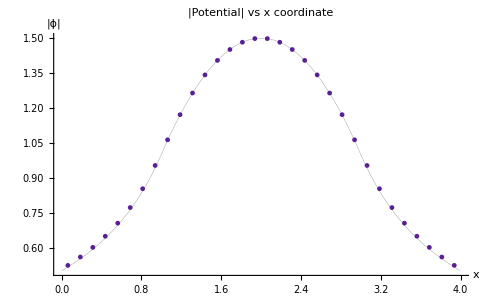

```mathematica
Show[Plot[-V[x-L/2],{x,0,L},PlotStyle->{Gray,Thickness[.0005]},AxesLabel->{HoldForm["x"],HoldForm["|ϕ|"]},PlotLabel->HoldForm["|Potential| vs x coordinate"]],plt[nz]=ListPlot[Transpose[{X,-A }],PlotStyle->{PointSize[.007],RGBColor@@RandomReal[1,3]}]]
```

### Plots for different values for n:

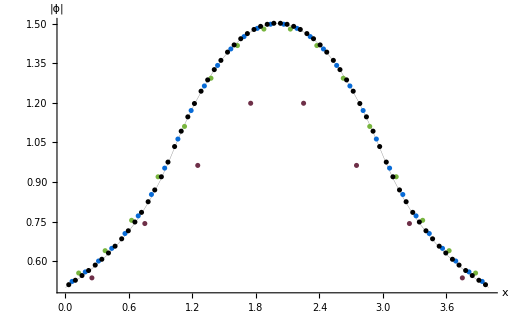

```mathematica
Show[Plot[-V[x-L/2],{x,0,L},PlotStyle->{Gray,Thickness[.0005]},AxesLabel->{HoldForm["x"],HoldForm["|ϕ|"]}],Table[plt[i],{i,{8,16,32,64(*,128*)}}]]
```

## Averaging radial potential

Calculating the zones within shells of radius 2jL/n and 2L(j+1)/n

```mathematica
Total[(L/2+(0.5 L)/nz-(# L)/nz)^2&/@{i,j,k}]
```

4.10089+(2.0625-i/8)^2+(2.0625-j/8)^2

```mathematica
grid=Flatten[Table[{Floor[Sqrt[1.0(i-nz/2)^2+(j-nz/2)^2+(k-nz/2)^2]],mSol[[i,j,k]]},{i,1,nz},{j,1,nz},{k,1,nz}],2];
```

Calculating average potential of all zones within a shell

```mathematica
Vr=Table[Mean[Select[grid,#[[1]]==j&][[All,2]]],{j,1,nz/2}];
```

The array Vr now contains the average radial potential measured over steps of 2L/n.

```mathematica
Vr//Length
```

16

## Plot of analytic vs numerical solution of average radial potential

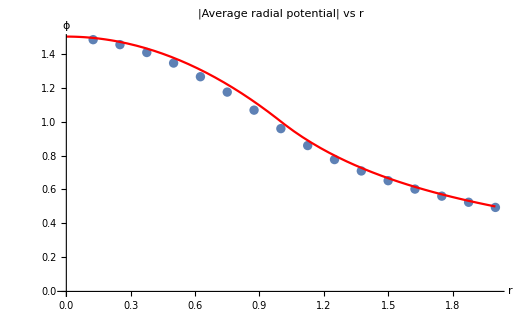

```mathematica
Show[ListPlot[Transpose[{Range[Length[Vr]]L/nz,Abs[Vr]}],AxesLabel->{HoldForm["r"],HoldForm["ϕ"]},PlotLabel->HoldForm["|Average radial potential| vs r"]],Plot[-V[x],{x,0,L/2},PlotStyle->Red]]
```